```mathematica
mat= Table[Import[NotebookDirectory[]<>"/"<>i<>"_HH1_32_0.0_1_0.001_"<>j<>".csv"][[2]][[1]],  {i,{"ER","BA", "WS"}},{j,{"0.0","1.0e-5","5.0e-5","0.0001","0.0005","0.001","0.005","0.01"}}];
```

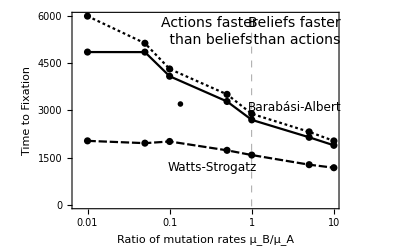

```mathematica
data1= Transpose[{{0.0,0.01,0.05,0.1,0.5,1,5,10},mat[[1]]}];
data2=Transpose[{{0.0,0.01,0.05,0.1,0.5,1,5,10},mat[[3]]}];
data3=Transpose[{{0.0,0.01,0.05,0.1,0.5,1,5,10},mat[[2]]}];
ListLogLinearPlot[{data1,data2,data3},Joined->True,Mesh->All,Frame->True,FrameStyle->Directive[Black,Thickness[0.0025]],GridLines->{{1}, None},GridLinesStyle->Directive[Gray, Dashed],PlotTheme->"Monochrome",
Epilog->{
Inset[Style["Actions faster\n than beliefs",14],{-1.2,5500}],
Inset[Style["Beliefs faster\n than actions",14],{1.2,5500}],
Inset[Style["Barabási-Albert",12],{1.2,3100}],
Inset[Style["Watts-Strogatz",12],{-1.1,1200}],
Inset[Style["Erdös-Rényi",12],{-2,3200}]},FrameLabel->{Style["Ratio of mutation rates μ_B/μ_A",Black,16],Style["Time to Fixation",Black,16]},Background->White]
```

```mathematica
Export[NotebookDirectory[]<>"time_fixation_networks.pdf",plot1];
```